# Report Projekt 1

Course code: IX1500
Date: 2025-09-15

Abdinasir Abdi, Abdabdi@kth.se
Jonas Sedig, Jonsed@kth.se

Uppgift 1: Vägar i

## Sammanfattning

### Uppgift

I denna uppgift modelleras en partikel i xy planet som rör sig enlig följade steg: 

 U :(m,n) → (m+1,n+1) (1)
 L :(m,n) → (m+1,n−1) (2)
 
Målet med uppgiften är att beräkna alla möjliga vägar från en startpunt (x, y) till en given slutpunkt (x’, y’). U omfattas som ett uppsteg medan L som ett nedsteg och varje väg är en följd av dessa två. Utöver det studeras fall med restriktioner: hur många vägar som minst rör eller korsar x-axeln, och hur många som alltid håller sig ovanför den.

### Result

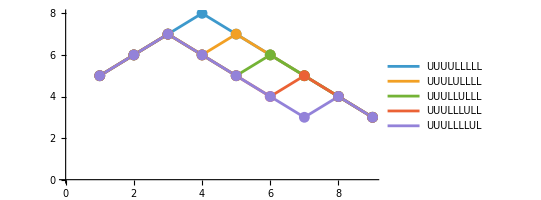

Figur 1: Några exempel på möjliga vägar

3.1 

A)  Varje väg från punkten (0,4) till (9,3) består av 9 steg, 4 uppsteg och 5 nedsteg. Totala antalet olika ordningar dessa steg ges av binomialkoefficienten  (9/4) = 126 vägar.

B)  Av alla möjliga vägar finns det totalt 9 vägar som berör eller passerar x-axel minste en gång.

C) Skillnaden mellan alla möjliga vägar och alla vägar som passerar rör eller korsar x-axeln, ger oss alla som aldrig berör.

126 - 9 = 117

D)  Det finns total 11 väagr från punkten (0,5) till (11,4) som aldrig rör eller korsar x-axeln

## Formler och ekvationer

Uppgiftens viktigaste formler kommer från grundläggande kombinatorik . Varje väg mellan två punkter i planet bestäms av en kombination uppsteg och nedsteg . Båda steg rör sig framåt i planet, åt höger i x - led, samtidigt som y - koordinaten förändras med + 1 respektive - 1.  

u +l = n,               u - l = y_1 -y_0 

Genom att lösa ekvationssystemet kan får man följande uttryck 

u =(n + (y_1 -y_0))/2

Slutligen kan antalet möjliga vägar beräknas genom binomialkoefficienten 

 Binomial[n, u]==(n!)/((n-u)! u!)

## Diskussion

Alla U är identiska sinsemellan, likaså alla L, och i samband med detta spelar det ingen roll vilken specifik U eller L som används. Det som är avgörande är ordningen i vilken stegen placeras. Två olika följder kan representera två olika vägar trots att det innehåller lika många U och L.

Problemet kan därmed beskrivas som en permutation av en multimängd, det vill säga att en mängd ordnas där flera element är identiska, med u kopior av U och l kopior av L. Det tolkas inte som en kombination med upprepning då antalet av varje typ av steg inte är fritt men fixerat. Antalet möjliga distinka arrangemang som uppstår när identiska element uppträder i bestämda mängder ges av följande: 

(n!)/(u! l!)

Eftersom vi bara har arrangemang av kopior för två typer av element U  och L, reduceras uttrycket till den vanliga binomialkoefficienten;

Binomial[n, u]

## Kod

```mathematica
ClearAll["`*"]
```

Kod för fråga a)

```mathematica
Binomial[9,4]
```

Kod för fråga b)

```mathematica
startPosY = 4;
n = 9;
u = 4;
l=  5;

(*Skapar en lista med 4st U och 5st L. join sätter ihop dem till en gemensam lista och Permutations skapar alla möjliga arrangemang/ordningar av dessa*)
allaV = Permutations[Join[Table["U", u], Table["L", l]]];

(*En funktion som räknar Y-koordinaten efter varje steg. "seq/" byter ut U mot +1 och L mot -1. Därmed summerar FoldList alla dessa steg en efter en från start y=4. Detta ger en lista med y värden längs vägen.*)
yLevels[seq_]:=FoldList[Plus,startPosY,seq/. {"U"->1,"L"->-1}];

(*yLevels[#] räknar ut alla y-värden sekvensen. MemberQ[.. O] kollar
ifall listan innehåller 0 och Select behåller de vägar där y = 0*)

vagarT=Select[allaV,MemberQ[yLevels[#],0]&];

Length[vagarT]
```

9

Kod för fråga c) Samma metod som i b-uppgiften, men ändrade värden.

```mathematica
startPosY = 5;
n = 11;
u = 5;
l=  6;

(*Skapar en lista med 5st U och .086st L. join sätter ihop dem till en gemensam lista och Permutations skapar alla möjliga arrangemang/ordningar av dessa*)
allaV = Permutations[Join[Table["U", u], Table["L", l]]];

(*En funktion som räknar Y-koordinaten efter varje steg. "seq/" byter ut U mot +1 och L mot -1. Därmed summerar FoldList alla dessa steg en efter en från start y=4. Detta ger en lista med y värden längs vägen.*)
yLevels[seq_]:=FoldList[Plus,startPosY,seq/. {"U"->1,"L"->-1}];

(*yLevels[#] räknar ut alla y-värden sekvensen. MemberQ[.. O] kollar
ifall listan innehåller 0 och Select behåller de vägar där y = 0*)

vagarT=Select[allaV,MemberQ[yLevels[#],0]&];

Length[vagarT]
```

11

Kod för Figur 1;

```mathematica
(*Start-och slutpunkter*)
start={0,4};
goal={9,3};

(*Subsets genererar delmängder som beskrive vilka positioner i sekvensen som ska vara U-steg,
resterande blir därmed L-steg. På detta viss skapas alla möjliga U/L sekvenser.*)
allaSteg=Subsets[Range[n],{u}]; (*u och n är redan definerade i tidigare uppgift*)

(*toSeq gör en positionlista till en sekvens och därmed körs den på alla positionsplatser i allaSteg*)
toSeq[pos_]:=Table[If[MemberQ[pos,i],"U","L"],{i,n}];
allaVagar=toSeq/@allaSteg;

(*Slutligen ritas några möjliga vägar*)
ListLinePlot[coords/@Take[allaVagar,5], (* Här går det att ändra antal*)
AxesOrigin->{0,0},
AspectRatio->1/2,
PlotRange->All,Mesh->All,
PlotLegends->(StringJoin/@Take[allaVagar,5])]
```

-Graphics-